```mathematica
ClearAll["Global`*"]
ClearSystemCache[]
```

```mathematica
Sfunc[dp_,ptot_,kp_,KMM_]:=(dp*ptot/kp)/(KMM+(dp*ptot/kp));
Rfunc[dm_,dmmu_,KMM_,mutot_,ptot_,dp_,kp_]:=1-1/(1+(dm+dmmu)/dm*mutot/(KMM+dp*ptot/kp));
fcm[dm_,R_,S_]:=dm*(1-R*S)/(1-R);

(*Actual Fano Factor for Regulated SyScem*)
fanofuncmuraw[kp_,ptot_,dp_,dm_,KMM_,dmmu_,mutot_,dmu_]:=Module[{R,S,cm,er0},
R=Rfunc[dm,dmmu,KMM,mutot,ptot,dp,kp];
     S=Sfunc[dp,ptot,kp,KMM];
cm=fcm[dm,R,S];
er0=1+kp/(1-R*S)/(dp+cm)+ptot/mutot*(R/(1-R*S))^2*(dp*cm)*(cm+dp+dmu)/((dp+cm)(cm+dmu)(dp+dmu));
Return[er0];]

fanofuncmurawandc1[kp_,ptot_,dp_,dm_,KMM_,dmmu_,mutot_,dmu_,nm_,nmu_]:=Module[{R,S,cm,er0,nu,nuctotv},
R=Rfunc[dm,dmmu,KMM,mutot,ptot,dp,kp];
     S=Sfunc[dp,ptot,kp,KMM];
cm=fcm[dm,R,S];
nu=dm*dp/kp*ptot;
er0=1+kp/(1-R*S)/(dp+cm)+ptot/mutot*(R/(1-R*S))^2*(dp*cm)*(cm+dp+dmu)/((dp+cm)(cm+dmu)(dp+dmu));
nuctotv=nu/(1-R)*nm+dmu*mutot*nmu;
Return[{er0,nuctotv}];]

(*Actual Fano Factor for Unregulated SyScem*)
fanounregfunc[kp_,dp_,dm_,ptot_]:=1+kp/(dm+dp);

(*Optimal Fano Factor for Regulated SyScem*)
foptfuncmuraw2[kp_,ptot_,dp_,dm_,KMM_,dmmu_,mutot_,dmu_]:=Module[{Rqq,Sqq,etaw,zetaw,Qw,smu1w,smu2w,eres2},Rqq=Rfunc[dm,dmmu,KMM,mutot,ptot,dp,kp];
Sqq=Sfunc[dp,ptot,kp,KMM];
etaw=(1-Rqq)/(Rqq)/(1-Sqq)^2;
zetaw=dm/(dm+dmmu);
Qw=etaw*Sqq/zetaw;
smu1w=Sqrt[(dmu^2 etaw+dm^2 (1+etaw)+dm dmu Qw+Sqrt[-4 dm^2 dmu etaw (dmu+dmu etaw+dm Qw)+(dmu^2 etaw+dm^2 (1+etaw)+dm dmu Qw)^2])/etaw]/Sqrt[2];
smu2w=Sqrt[(dmu^2 etaw+dm^2 (1+etaw)+dm dmu Qw-Sqrt[-4 dm^2 dmu etaw (dmu+dmu etaw+dm Qw)+(dmu^2 etaw+dm^2 (1+etaw)+dm dmu Qw)^2])/etaw]/Sqrt[2];
eres2=(dm+dp+kp+(dm^2 kp (((dm+dmu) dp ((-dm-dmu) (dm-dp) (dm+dp)-(4 dm (dmu+dp) (dm+smu1w) (dm+smu2w))/(dp+smu1w)))/((dm+smu1w)^2 (dm+smu2w)^2)+(dm (dmu+dp) ((dmu+dp) (-dm^2+dp^2)+(4 (dm+dmu) dp (dp+smu1w) (dp+smu2w))/(dm+smu1w)))/((dp+smu1w)^2 (dp+smu2w)^2)))/((dm-dp)^3 etaw))/(dm+dp);
Return[eres2];]
fanogap[kp_,ptot_,dp_,dm_,KMM_,dmmu_,mutot_,dmu_]:=Module[{cm,R,S,ress},R=Rfunc[dm,dmmu,KMM,mutot,ptot,dp,kp];
S=Sfunc[dp,ptot,kp,KMM];
cm=fcm[dm,R,S];
ress=(((cm+dm) (cm+dp) (dm+dp)+dm (cm+dm+2 dp) kp))/((cm+dm) (cm+dp) (dm+dp));
Return[ress];]
ewk[kp_,ptot_,dp_,dm_,KMM_,dmmu_,mutot_,dmu_]:=Module[{ff0,ffmu,ffgap,eres,ffdenom},ff0=fanounregfunc[kp,dp,dm,ptot];
ffmu=fanofuncmuraw[kp,ptot,dp,dm,KMM,dmmu,mutot,dmu];
ffgap=fanogap[kp,ptot,dp,dm,KMM,dmmu,mutot,dmu];
ffdenom=ff0-2*ffgap+ffmu;
eres=1-(ff0-ffgap)^2/ff0/ffdenom;
Return[eres];]
ewkopt[kp_,ptot_,dp_,dm_,KMM_,dmmu_,mutot_,dmu_]:=Module[{ff0,ffopt,eres},ff0=fanounregfunc[kp,dp,dm,ptot];
ffopt=foptfuncmuraw2[kp,ptot,dp,dm,KMM,dmmu,mutot,dmu];
eres=(ffopt-1)/(ff0-1);
Return[eres];]
gfact[kp_,ptot_,dp_,dm_,KMM_,dmmu_,mutot_,dmu_]:=Module[{ff0,ffmu,ffgap,eres,ffdenom,ffpepm},ff0=fanounregfunc[kp,dp,dm,ptot];
ffmu=fanofuncmuraw[kp,ptot,dp,dm,KMM,dmmu,mutot,dmu];
ffgap=fanogap[kp,ptot,dp,dm,KMM,dmmu,mutot,dmu];
ffdenom=ff0-2*ffgap+ffmu;
eres=ffdenom/(ff0-ffgap);
Return[eres];]
sigp0pe[kp_,ptot_,dp_,dm_,KMM_,dmmu_,mutot_,dmu_]:=Module[{ff0,ffmu,ffgap,eres,ffdenom,ffpepm},ff0=fanounregfunc[kp,dp,dm,ptot];
ffmu=fanofuncmuraw[kp,ptot,dp,dm,KMM,dmmu,mutot,dmu];
ffgap=fanogap[kp,ptot,dp,dm,KMM,dmmu,mutot,dmu];
ffdenom=ff0-2*ffgap+ffmu;
eres=(ff0-ffgap);
Return[eres];]
sigpepe[kp_,ptot_,dp_,dm_,KMM_,dmmu_,mutot_,dmu_]:=Module[{ff0,ffmu,ffgap,eres,ffdenom,ffpepm},ff0=fanounregfunc[kp,dp,dm,ptot];
ffmu=fanofuncmuraw[kp,ptot,dp,dm,KMM,dmmu,mutot,dmu];
ffgap=fanogap[kp,ptot,dp,dm,KMM,dmmu,mutot,dmu];
ffdenom=ff0-2*ffgap+ffmu;
eres=(ffdenom);
Return[eres];]
gfreeFANO[kp_,ptot_,dp_,dm_,KMM_,dmmu_,mutot_,dmu_]:=Module[{ff0,sigpepev,sigp0pev,eres,gfactv},
ff0=fanounregfunc[kp,dp,dm,ptot];
sigp0pev=sigp0pe[kp,ptot,dp,dm,KMM,dmmu,mutot,dmu];
sigpepev=sigpepe[kp,ptot,dp,dm,KMM,dmmu,mutot,dmu];
gfactv=gfact[kp,ptot,dp,dm,KMM,dmmu,mutot,dmu];
eres=(sigpepev-2*gfactv*sigp0pev+gfactv^2*ff0)/gfactv^2;
Return[eres];]
(*----------------------------------------------*)
```

```mathematica
(*Functions for Minimization*)
(*Non-filter phase line*)
mutotfilter[kp_,ptot_,dp_,dm_,KMMv_,dmmu_,dmu_,nm_,nmu_]:=Module[{fanoREG,fanoUNREG,mutotsolvemat,res,mutotv,zetav,nuctes},
zetav=dm/(dm+dmmu);
fanoREG=Simplify[fanofuncmuraw[kp,ptot,dp,dm,KMMv,dmmu,mutotv,dmu]];
fanoUNREG=1+kp/dm/(1+dp/dm);
mutotsolvemat=NSolve[fanoREG==fanoUNREG && mutotv>0.5,mutotv];
If[Length[mutotsolvemat]>0,res=mutotv/.mutotsolvemat[[1]],res=0];
nuctes=totalnuctfunc[KMMv,kp,res,dp,ptot,zetav,dm,dmu,nm,nmu];
Return[{KMMv,res,nuctes}];]
mutotfilternum[kp_,ptot_,dp_,dm_,KMMv_,dmmu_,dmu_,nm_,nmu_,KMMc_,pbaRc_]:=Module[{fanoREG,fanoUNREG,mutotsolvemat,res,mutotv,zetav,nuctes,c0,Si,Sc,gami,},
zetav=dm/(dm+dmmu);
fanoREG=Simplify[fanofuncmuraw[kp,ptot,dp,dm,KMMv,dmmu,mutotv,dmu]];
fanoUNREG=1+kp/dm/(1+dp/dm);
mutotsolvemat=NSolve[fanoREG==fanoUNREG && mutotv>0.5,mutotv];
If[Length[mutotsolvemat]>0,res=mutotv/.mutotsolvemat[[1]],res=0];
Si=Sfunc[dp,ptot,kp,KMMv];
Sc=Sfunc[dp,pbaRc,kp,KMMc];
gami=(1-Si)*Sc/(1-Sc);
res=res*(1+gami);
nuctes=totalnuctfuncnum[KMMv,kp,res,dp,ptot,zetav,dm,dmu,nm,nmu,KMMc,pbaRc];
c0=nm*dm*dp/kp*(ptot+pbaRc);
Return[{KMMv,res,nuctes,nuctes/c0}];]

(*Error(actual) minimizing K value at fixed nucleotide number c1*)
KMMminndagger[c1_,kp_,ptot_,dmmu_,dp_,dm_,dmu_,nm_,nmu_]:=Module[{sac,KMMcand,sacmat,KMMresf,mutotvar,zetav,mutotval,fanores,KMMv,mutinf,Rget,Sget,c0},
zetav=dm/(dm+dmmu);
mutotvar=fixNuctgetmutot[c1,kp,KMMv,dp,ptot,zetav,dm,dmu,nm,nmu];
sac=fanofuncmuraw[kp,ptot,dp,dm,KMMv,dmmu,mutotvar,dmu];
KMMcand=2*dp/kp*ptot;
sacmat=FindMinimum[{sac,KMMv>0},{KMMv,KMMcand},PrecisionGoal->12][[2]];
KMMresf=KMMv/.sacmat[[1]];
mutotval=fixNuctgetmutot[c1,kp,KMMresf,dp,ptot,zetav,dm,dmu,nm,nmu];
fanores=fanofuncmuraw[kp,ptot,dp,dm,KMMresf,dmmu,mutotval,dmu];
mutinf=-1/2*Log2[ewk[kp,ptot,dp,dm,KMMresf,dmmu,mutotval,dmu]];
Rget=Rfunc[dm,dmmu,KMMresf,mutotval,ptot,dp,kp];
Sget=Sfunc[dp,ptot,kp,KMMresf];
c0=nm*dm*dp/kp*ptot;
Return[{KMMresf,mutotval,c1,fanores,mutinf,Rget,Sget,c1/c0}];]
(*Error(actual) minimizing K value at fixed nucleotide number c1*)
KMMminndaggernum[c1_,kp_,ptot_,dmmu_,dp_,dm_,dmu_,nm_,nmu_,KMMc_,pbaRc_]:=Module[{sac,KMMcand,sacmat,KMMresf,mutotvar,zetav,mutotval,fanores,KMMv,mutinf,Rget,Sget,c0,gamivar,gamcvar,gamival,gamcval,mnull},
zetav=dm/(dm+dmmu);
{gamivar,gamcvar,mutotvar,mnull}=fixNuctgetgammsnum[c1,kp,KMMv,dp,ptot,zetav,dm,dmu,nm,nmu,KMMv,pbaRc];
sac=fanofuncmuraw[kp,ptot,dp,dm,KMMv,dmmu,mutotvar/(1+gamivar),dmu];
KMMcand=2*dp/kp*ptot;
sacmat=FindMinimum[{sac,KMMv>0},{KMMv,KMMcand},PrecisionGoal->15][[2]];
KMMresf=KMMv/.sacmat[[1]];
mutotval=fixNuctgetmutotnum[c1,kp,KMMresf,dp,ptot,zetav,dm,dmu,nm,nmu,KMMresf,pbaRc];
{gamival,gamcval,mutotval,mnull}=fixNuctgetgammsnum[c1,kp,KMMresf,dp,ptot,zetav,dm,dmu,nm,nmu,KMMresf,pbaRc];
fanores=fanofuncmuraw[kp,ptot,dp,dm,KMMresf,dmmu,mutotval/(1+gamival),dmu];
mutinf=-1/2*Log2[ewk[kp,ptot,dp,dm,KMMresf,dmmu,mutotval/(1+gamival),dmu]];
Rget=Rfunc[dm,dmmu,KMMresf,mutotval/(1+gamival),ptot,dp,kp];
Sget=Sfunc[dp,ptot,kp,KMMresf];
c0=nm*dm*dp/kp*(ptot+pbaRc);
Return[{KMMresf,mutotval,c1,fanores,mutinf,Rget,Sget,c1/c0,c1-c0}];]


(*Error(optimal) minimizing K value at fixed nucleotide number c1*)
KMMminndaggerOPT[c1_,kp_,ptot_,dmmu_,dp_,dm_,dmu_,nm_,nmu_]:=Module[{sac,KMMcand,sacmat,KMMresf,mutotvar,zetav,mutotval,fanores,KMMv,mutinf},
zetav=dm/(dm+dmmu);
mutotvar=fixNuctgetmutot[c1,kp,KMMv,dp,ptot,zetav,dm,dmu,nm,nmu];
sac=foptfuncmuraw2[kp,ptot,dp,dm,KMMv,dmmu,mutotvar,dmu];
KMMcand=2*dp/kp*ptot;
sacmat=FindMinimum[{sac,KMMv>0},{KMMv,KMMcand},PrecisionGoal->6][[2]];
KMMresf=KMMv/.sacmat[[1]];
mutotval=fixNuctgetmutot[c1,kp,KMMresf,dp,ptot,zetav,dm,dmu,nm,nmu];
fanores=foptfuncmuraw2[kp,ptot,dp,dm,KMMresf,dmmu,mutotval,dmu];
mutinf=-1/2*Log2[ewkopt[kp,ptot,dp,dm,KMMresf,dmmu,mutotval,dmu]];
Return[{KMMresf,mutotval,c1,fanores,mutinf}];]

(*Error(optimal) minimizing K value at fixed nucleotide number c1*)
KMMminndaggerOPTnum[c1_,kp_,ptot_,dmmu_,dp_,dm_,dmu_,nm_,nmu_,KMMc_,pbaRc_]:=Module[{sac,KMMcand,sacmat,KMMresf,mutotvar,zetav,mutotval,fanores,KMMv,mutinf,Rget,Sget,c0,gamivar,gamcvar,gamival,gamcval,mnull},
zetav=dm/(dm+dmmu);
{gamivar,gamcvar,mutotvar,mnull}=fixNuctgetgammsnum[c1,kp,KMMv,dp,ptot,zetav,dm,dmu,nm,nmu,KMMv,pbaRc];
sac=foptfuncmuraw2[kp,ptot,dp,dm,KMMv,dmmu,mutotvar/(1+gamivar),dmu];
KMMcand=2*dp/kp*ptot;
sacmat=FindMinimum[{sac,KMMv>0},{KMMv,KMMcand},PrecisionGoal->12][[2]];
KMMresf=KMMv/.sacmat[[1]];
mutotval=fixNuctgetmutotnum[c1,kp,KMMresf,dp,ptot,zetav,dm,dmu,nm,nmu,KMMresf,pbaRc];
{gamival,gamcval,mutotval,mnull}=fixNuctgetgammsnum[c1,kp,KMMresf,dp,ptot,zetav,dm,dmu,nm,nmu,KMMresf,pbaRc];
fanores=foptfuncmuraw2[kp,ptot,dp,dm,KMMresf,dmmu,mutotval/(1+gamival),dmu];
mutinf=-1/2*Log2[ewkopt[kp,ptot,dp,dm,KMMresf,dmmu,mutotval/(1+gamival),dmu]];
Rget=Rfunc[dm,dmmu,KMMresf,mutotval/(1+gamival),ptot,dp,kp];
Sget=Sfunc[dp,ptot,kp,KMMresf];
c0=nm*dm*dp/kp*(ptot+pbaRc);
Return[{KMMresf,mutotval,c1,fanores,mutinf,Rget,Sget,c1/c0,c1-c0}];]

(*K value at all parameters and nucleotide number c1 fixed*)
fixNuctgetKMM[c1_,kp_,mutot_,dp_,ptot_,zeta_,dm_,dmu_,nm_,nmu_]:=Module[{dmmu,nu,KMMresv},
dmmu=(dm-dm zeta)/zeta;
nu=dm*dp/kp*ptot;

KMMresv=(dm kp mutot nm nu+dmmu kp mutot nm nu-c1 dm dp ptot+dm dmu dp mutot nmu ptot+dm dp nm nu ptot)/(dm kp (c1-dmu mutot nmu-nm nu));Return[KMMresv];]

(*microRNA value at all parameters and nucleotide number c1 fixed*)
fixNuctgetmutot[c1_,kp_,KMM_,dp_,ptot_,zeta_,dm_,dmu_,nm_,nmu_]:=Module[{dmmu,nu,muresv,muresvmat,Rv},
dmmu=(dm-dm zeta)/zeta;
nu=dm*dp/kp*ptot;
Rv=Rfunc[dm,dmmu,KMM,mutotval,ptot,dp,kp];
muresvmat=Solve[c1==nu/(1-Rv)*nm+dmu*mutotval*nmu,mutotval];
muresv=mutotval/.muresvmat[[1]];
Return[muresv];];

(*microRNA value at all parameters and nucleotide number c1 fixed*)
fixNuctgetmutotnum[c1_,kp_,KMM_,dp_,ptot_,zeta_,dm_,dmu_,nm_,nmu_,KMMc_,pbarc_]:=Module[{dmmu,compi,compt,St,Sc,gamt, gamc,nu,muresv,muresvmat,Rt,Rc},
dmmu=(dm-dm zeta)/zeta;
nu=dm*dp/kp*ptot;
St=Sfunc[dp,ptot,kp,KMM];
Sc=Sfunc[dp,pbarc,kp,KMMc];
gamt=(1-St)*Sc/(1-Sc);
gamc=(1-Sc)*St/(1-St);
Rc=Rfunc[dm,dmmu,KMM,mutotval/(1+gamc),pbarc,dp,kp];
Rt=Rfunc[dm,dmmu,KMM,mutotval/(1+gamt),ptot,dp,kp];
muresvmat=Solve[c1==nu/(1-Rt)*nm+dmu*mutotval*nmu+dm*dp/kp*pbarc/(1-Rc)*nm,mutotval];
muresv=mutotval/.muresvmat[[1]];
Return[muresv];];

(*microRNA value at all parameters and nucleotide number c1 fixed*)
fixNuctgetgammsnum[c1_,kp_,KMM_,dp_,ptot_,zeta_,dm_,dmu_,nm_,nmu_,KMMc_,pbarc_]:=Module[{dmmu,compi,compt,St,Sc,gamt, gamc,nu,muresv,muresvmat,Rt,Rc},
dmmu=(dm-dm zeta)/zeta;
nu=dm*dp/kp*ptot;
St=Sfunc[dp,ptot,kp,KMM];
Sc=Sfunc[dp,pbarc,kp,KMMc];
gamt=(1-St)*Sc/(1-Sc);
gamc=(1-Sc)*St/(1-St);
Rc=Rfunc[dm,dmmu,KMM,mutotval/(1+gamc),pbarc,dp,kp];
Rt=Rfunc[dm,dmmu,KMM,mutotval/(1+gamt),ptot,dp,kp];
muresvmat=Solve[c1==nu/(1-Rt)*nm+dmu*mutotval*nmu+dm*dp/kp*pbarc/(1-Rc)*nm,mutotval];
muresv=mutotval/.muresvmat[[1]];
Return[{gamt,gamc,muresv,muresv/(1+gamt)}];];
(*total nucleotide number spent per unit time*)totalnuctfunc[KMM_,kp_,mutot_,dp_,ptot_,zeta_,dm_,dmu_,nm_,nmu_]:=Module[{dmmu,nu,nuctot},dmmu=(dm-dm zeta)/zeta;
nu=dm*dp/kp*ptot;nuctot=nu*(1/(1+((dm+dmmu) mutot)/(dm (KMM+(dp ptot)/kp))))^(-1)*nm+nmu*dmu*mutot;Return[nuctot];]
totalnuctfuncnum[KMM_,kp_,mutot_,dp_,ptot_,zeta_,dm_,dmu_,nm_,nmu_,KMMc_,pbarc_]:=Module[{dmmu,nu,nuctot,St,Sc,gamt,gamc,Rt,Rc},dmmu=(dm-dm zeta)/zeta;
nu=dm*dp/kp*ptot;
St=Sfunc[dp,ptot,kp,KMM];
Sc=Sfunc[dp,pbarc,kp,KMMc];
gamt=(1-St)*Sc/(1-Sc);
gamc=(1-Sc)*St/(1-St);
Rc=Rfunc[dm,dmmu,KMM,mutot/(1+gamc),pbarc,dp,kp];
Rt=Rfunc[dm,dmmu,KMM,mutot/(1+gamt),ptot,dp,kp];nuctot=nu/(1-Rt)*nm+dmu*mutot*nmu+dm*dp/kp*pbarc/(1-Rc)*nm;Return[nuctot];]
totalnuctfuncnumwithFano[KMM_,kp_,mutot_,dp_,ptot_,zeta_,dm_,dmu_,nm_,nmu_,KMMc_,pbaRc_]:=Module[{dmmu,nu,nuctot,St,Sc,gamt,gamc,Rt,Rc,fanores,mutotval,c0},dmmu=(dm-dm zeta)/zeta;
nu=dm*dp/kp*ptot;
St=Sfunc[dp,ptot,kp,KMM];
Sc=Sfunc[dp,pbaRc,kp,KMMc];
gamt=(1-St)*Sc/(1-Sc);
gamc=(1-Sc)*St/(1-St);
Rc=Rfunc[dm,dmmu,KMM,mutot/(1+gamc),pbaRc,dp,kp];
Rt=Rfunc[dm,dmmu,KMM,mutot/(1+gamt),ptot,dp,kp];nuctot=nu/(1-Rt)*nm+dmu*mutot*nmu+dm*dp/kp*pbaRc/(1-Rc)*nm;
mutotval=fixNuctgetmutotnum[nuctot,kp,KMM,dp,ptot,zeta,dm,dmu,nm,nmu,KMMc,pbaRc];
fanores=fanofuncmuraw[kp,ptot,dp,dm,KMM,dmmu,mutotval,dmu];
c0=nm*dm*dp/kp*(ptot+pbaRc);Return[{Log10[nuctot/c0],fanores}];]
```

```mathematica
(*--------------------end Functions for Minimization--------------------------*)
```

```mathematica
(*Parameters per hour*)
kp1=140;(*translation rate *)
dp1=0.022;(*degradation rate of protein*)
ptot1single=200000;(*Sceady-Scate mean protein level*)
dm0=0.11;(*degradation rate of mRNA*)
dmmu1=3*dm0;(*extra degradation rate of mRNA in complex*) (*!!!! note that in manuscript dmmu -> dmmu1+dm0*)
dmu1=0.8*dm0;(*degradation rate of microRNA*)
Kmin=0;
Ky=Kmin;
KMMcv=1000;(*competitor KMM*) (*not used*)
nm0=7000;(*nucleotide number of mRNAs*)
nmu0=100;(*nucleotide number of microRNAs*)
avagadro=6.022*10^(23);
cellvol=2*10^(-12);
noconv=1/avagadro/cellvol*10^9; (*in nM*)
ppfactor=2.17;(*phospate bonds hydrolized per nucleotide*)
fanoUNREG00=fanounregfunc[kp1,dp1,dm0,ptot1];
c00v=nm0*dm0*dp1/kp1*(ptot1+pbarcv0);
(*end Parameters*)
```

FindMinimum::acceptlev: Solved to acceptable level.

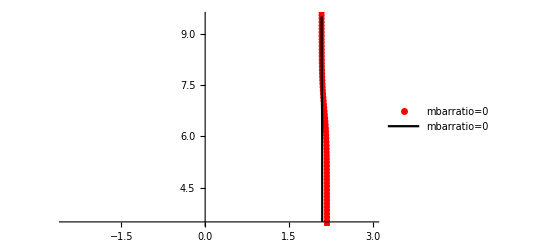

Null

```mathematica
(*Min Error Plots*)
mbarratio0=0;(*competitor/target mRNA levels*) (* keep this zero increase ptot1 prefactor for multi-targets*)
pbarcv0=0*mbarratio0*ptot1;
ptot1=100*ptot1single;  (*upscale for no of targets*)
n00=nm0*dm0*dp1/kp1*(ptot1+pbarcv0);
tabKmin2nuctLIN0=Table[KMMminndaggernum[n00+10^ynuct,kp1,ptot1,dmmu1,dp1,dm0,dmu1,nm0,nmu0,KMMcv,pbarcv0],{ynuct,3.0,9.5,.1}];
tabKmin2nuctLIN0opt=Table[KMMminndaggerOPTnum[n00+10^ynuct,kp1,ptot1,dmmu1,dp1,dm0,dmu1,nm0,nmu0,KMMcv,pbarcv0],{ynuct,3.0,9.5,.1}];
tabErmin2nuct0=Table[{Log10[tabKmin2nuctLIN0[[ii,1]]*noconv],Log10[ppfactor*tabKmin2nuctLIN0[[ii,9]]]},{ii,1,Length[tabKmin2nuctLIN0]}];
tabErmin2nuct0opt=Table[{Log10[tabKmin2nuctLIN0opt[[ii,1]]*noconv],Log10[ppfactor*tabKmin2nuctLIN0opt[[ii,9]]]},{ii,1,Length[tabKmin2nuctLIN0opt]}];
pErmin2nuct0=ListPlot[tabErmin2nuct0,PlotRange->{{-2.5,3},{3.5,9.5}},PlotStyle->Red,PlotLegends->{Row@{"mbarratio=", mbarratio0 },Red}];
pErmin2nuct0opt=ListPlot[tabErmin2nuct0opt,PlotRange->{{-2.5,3},{3.5,9.5}},PlotStyle->Black,Joined->True,PlotLegends->{Row@{"mbarratio=", mbarratio0 },Black}];
Show[pErmin2nuct0,pErmin2nuct0opt]
```

```mathematica
(*Minimum achievable Fano factor*)
tabFmin2nuct0=Table[{Log10[ppfactor*tabKmin2nuctLIN0[[ii,9]]],(tabKmin2nuctLIN0[[ii,4]]-1)/(fanoUNREG00-1)},{ii,1,Length[tabKmin2nuctLIN0]}];
tabFmin2nuct0opt=Table[{Log10[ppfactor*tabKmin2nuctLIN0opt[[ii,9]]],(tabKmin2nuctLIN0opt[[ii,4]]-1)/(fanoUNREG00-1)},{ii,1,Length[tabKmin2nuctLIN0opt]}];
tabFmin2nuct0diff=Table[{Log10[ppfactor*tabKmin2nuctLIN0opt[[ii,9]]],(tabKmin2nuctLIN0[[ii,4]]-tabKmin2nuctLIN0opt[[ii,4]])/(fanoUNREG00-1)},{ii,1,Length[tabKmin2nuctLIN0opt]}];
```

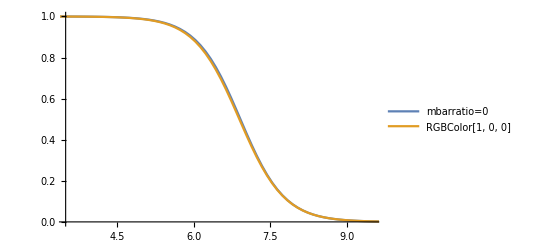

```mathematica
pFmin2nuct0=ListPlot[{tabFmin2nuct0,tabFmin2nuct0opt},PlotRange->{{3.5,9.5},{0,1}},Joined->True,PlotLegends->{Row@{"mbarratio=", mbarratio0 },Red}]
```

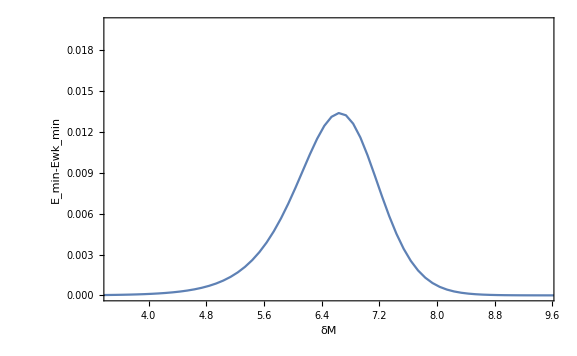

```mathematica
pFmin2nuct0diff=ListPlot[{tabFmin2nuct0diff},PlotRange->{{3.5,9.5},{0,.02}},Joined->True,Frame->True,FrameLabel->{"δM","E_min-Ewk_min"}]
```

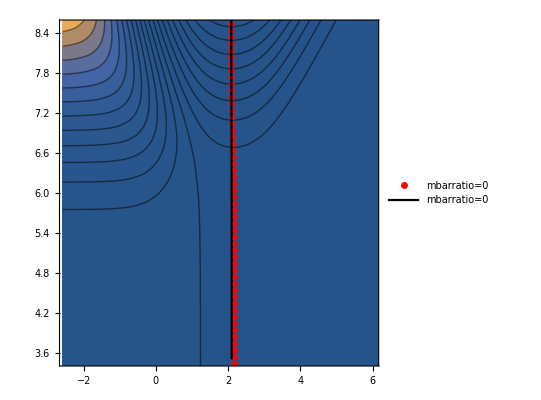

Null

```mathematica
(*Contour Plots*)(*functions always calculate Fano factor, here (FR-1)/(F0-1) contours (yet, almost identical with FR/F0 contours) *)
tabContFano=Flatten[Table[{yKmmvar+Log10[noconv],Log10[ppfactor*(10^ynuct)],(fanofuncmuraw[kp1,ptot1,dp1,dm0,10^yKmmvar,dmmu1,fixNuctgetgammsnum[n00+10^ynuct,kp1,10^yKmmvar,dp1,ptot1,dm0/(dm0+dmmu1),dm0,dmu1,nm0,nmu0,10^yKmmvar,pbarcv0][[4]],dmu1]-1)/(fanoUNREG00-1)},{yKmmvar,0.5,9.5,0.1},{ynuct,3.0,8.5,0.1}],1];
pcontourFano=ListContourPlot[tabContFano,Contours->Table[10^x,{x,-3,3,.2}],PlotRange->All];
Show[pcontourFano,pErmin2nuct0,pErmin2nuct0opt,PlotRange->{{-2.5,6},{3.5,8.5}}]
```

```mathematica
(*to get output data for matplotlib*)
tabContFanop=Table[{noconv*10^yKmmvar,ppfactor*(10^ynuct),fanofuncmuraw[kp1,ptot1,dp1,dm0,10^yKmmvar,dmmu1,fixNuctgetgammsnum[n00+10^ynuct,kp1,10^yKmmvar,dp1,ptot1,dm0/(dm0+dmmu1),dm0,dmu1,nm0,nmu0,10^yKmmvar,pbarcv0][[4]],dmu1]/fanoUNREG00},{yKmmvar,0.5,9.5,0.1},{ynuct,3.0,9.5,0.1}];
dx=Dimensions[tabContFanop][[1]];
dy=Dimensions[tabContFanop][[2]];
tabContFx=Table[noconv*10^yKmmvar,{yKmmvar,0.5,9.5,0.1}];
tabContFy=Table[ppfactor*(10^ynuct),{ynuct,3.0,9.5,0.1}];
tabContFz=Table[tabContFanop[[ii,jj,3]],{ii,1,dx},{jj,1,dy}];
```

```mathematica
(*Data Export*)
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"mirPD1minC2WKt100.txt"}],tabErmin2nuct0opt,"Table"];
Export[FileNameJoin[{NotebookDirectory[],"mirPD1minC2t100.txt"}],tabErmin2nuct0,"Table"];
Export[FileNameJoin[{NotebookDirectory[],"mirPD1FxC2t100.txt"}],tabContFx,"Table"];
Export[FileNameJoin[{NotebookDirectory[],"mirPD1FyC2t100.txt"}],tabContFy,"Table"];
Export[FileNameJoin[{NotebookDirectory[],"mirPD1FzC2t100.txt"}],Transpose[tabContFz],"Table"];
```

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"mirInfoC3WK.txt"}],tabInuct0opt,"Table"];
Export[FileNameJoin[{NotebookDirectory[],"mirElastC4.txt"}],tabElast,"Table"];
Export[FileNameJoin[{NotebookDirectory[],"mirElastC5vsR.txt"}],tabElastvsR,"Table"];*)
Export[FileNameJoin[{NotebookDirectory[],"mirErrWKt100.txt"}],tabFmin2nuct0opt,"Table"];
Export[FileNameJoin[{NotebookDirectory[],"mirErrt100.txt"}],tabFmin2nuct0,"Table"];
```

## EXTRA OBSERVABLES: ELASTICITY, MUTUAL INFORMATION

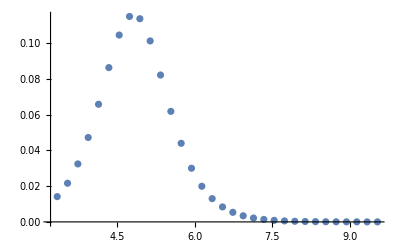

```mathematica
(*Elasticity at minimum achievable Fano factor*)
tabdiffF=Differences[tabFmin2nuct0];
tabElast=Table[{Log10[ppfactor*tabKmin2nuctLIN0[[ii,9]]],-tabdiffF[[ii,2]]},{ii,1,Length[tabdiffF]}];
tabElastvsR=Table[{tabKmin2nuctLIN0[[ii,6]],-tabdiffF[[ii,2]]},{ii,1,Length[tabdiffF]}];
ListPlot[tabElast]
```

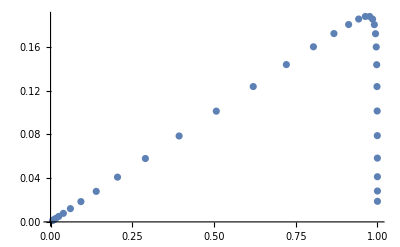

```mathematica
ListPlot[tabElastvsR]
```

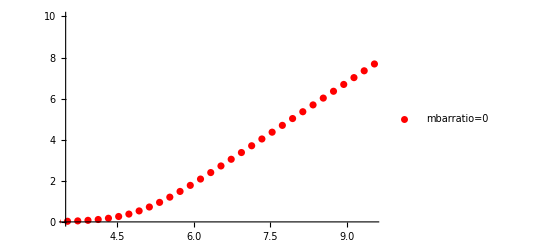

```mathematica
tabInuct0opt=Table[{Log10[ppfactor*tabKmin2nuctLIN0opt[[ii,9]]],tabKmin2nuctLIN0opt[[ii,5]]},{ii,1,Length[tabKmin2nuctLIN0opt]}];
pInuct0opt=ListPlot[tabInuct0opt,PlotRange->{{3.5,9.5},{0,10}},PlotStyle->Red,PlotLegends->{Row@{"mbarratio=", mbarratio0 },Red}]
```